# Impact of Urban Design on Quality of Life

## Intro

Most of the population around the globe is now concentrated in cities. There are around 2 dozens urban areas with populations exceeding 10 million people, but we still fail to quantify the influence of various aspects of urban design on the quality of life.
This work is a stepping stone in that direction.

## What is quality of life?

This is a very non-trivial question and we are not going to answer it in this work. Instead we will define a very simple approximation of quality of life as average sentiment across Tweets related to that specific city.

```mathematica
EstimateSentimentWL[sentence_String] := Module[{probs, pPos, pNeu, pNeg, resultPositivness, resultCertainity},
	probs = Classify["Sentiment", sentence, "Probabilities"];
	pPos = Lookup[probs, "Positive"];
	pNeu = Lookup[probs, "Neutral"];
	pNeg = Lookup[probs, "Negative"];
	resultPositivness = (pPos + pNeu * 0.5);
	resultCertainity = Max[probs];
	{resultPositivness,resultCertainity}
];
EstimateSentiments[sentences_, func_] := Map[({#, func[#]}) &, sentences];
EstimateSentiments[sentences_] := EstimateSentiments[sentences, EstimateSentimentWL];
EstimateQualityOfLifeWSentiment[data_] := Module[{sentences, tweetsWSentiments, sentimentsWCertainity, meanPositivness, meanCertainty},
	sentences = data⟦All, "Text"⟧;
	tweetsWSentiments = EstimateSentiments[sentences];
	sentimentsWCertainity = tweetsWSentiments⟦All, 2⟧;
	meanPositivness = MeanAround[sentimentsWCertainity⟦All, 1⟧];
	meanCertainty = MeanAround[sentimentsWCertainity⟦All, 2⟧];
	{meanPositivness, meanCertainty}
];

AssociationKeyRename[a_, old_ -> new_] /; KeyExistsQ[a, old] := KeyDrop[old] @ Append[a, new -> a[old]];
AssociationFromPair[strAndNum_List] := strAndNum⟦1⟧ -> strAndNum⟦2⟧;
AssociationsFromPair[keys_List, vals_List] := MapThread[(#1 -> #2) &, {keys, vals}];
RangeMakeAround[num_Integer, delta_Integer] := Range[num - delta, num + delta];
NomalizeNumber[number_Integer] := number;
NomalizeNumber[number_Real] := number;
NomalizeNumber[number_List] := number⟦1⟧;
NomalizeNumber[number_Quantity] := QuantityMagnitude[number];
NomalizeNumber[number_] := 0;
RescaleIntoInterval[numbers_List, numberNewSmallest_, numberNewLargest_] := Map[(# * (numberNewLargest - numberNewSmallest) + numberNewSmallest) &, Rescale[numbers]];
RescaleIntoInterval[numbers_List] := RescaleIntoInterval[numbers, 0.5, 0.95];

ColorsFindInImage[imgPixels_List, colors_List] := Flatten[Join[Map[(Position[imgPixels, #]) &, colors]]];
ColorsMakeShade[redVals_List, greenVals_List, blueVals_List] := Tuples[{redVals, greenVals, blueVals, { 255 }}];
ColorsMakeShade[red_Integer, green_Integer, blue_Integer, delta_Integer] := ColorsMakeShade[RangeMakeAround[red, delta],RangeMakeAround[green, delta],RangeMakeAround[blue, delta]];
ColorsMakeShade[grey_Integer, delta_Integer] := ColorsMakeShade[grey, grey, grey, delta];
ColorMake[r_,g_,b_] := RGBColor[r/255, g/255, b/255];
ColorMake[parts_List] := ColorMake[parts⟦1⟧, parts⟦2⟧, parts⟦3⟧];

EqualizeImages[imgs_List] := Module[{smallestW, smallestH, sizes},
	sizes = Map[ImageDimensions, imgs];
	smallestW = Min[sizes⟦All, 1⟧];
	smallestH = Min[sizes⟦All, 2⟧];
	Map[ImageCrop[#, {smallestW, smallestH}] &, imgs]
];
MapReconstructFromImages[imgs_List] := Module[{cntSide, imgsTable}, 
	cntSide = Sqrt[Length[imgs]];
	imgsTable = ArrayReshape[imgs, {cntSide,cntSide}];
	ImageAssemble[imgsTable]
];
```

## Which regions are we going to analyze?

rer

```mathematica
constantDirectory = "/Users/ashvardanian/CodeMine/WolframSummer19";
constantPathTweets = StringJoin[{constantDirectory, "/Data/Tweets"}];
constantPathFeatures = StringJoin[{constantDirectory, "/Data/Features"}];
constantPathMaps = StringJoin[{constantDirectory, "/Data/Maps"}];
constantPathSatellites = StringJoin[{constantDirectory, "/Data/Satellites"}];
constantCityDiameterKM = 10;
constantCityGridSize = 5;
constantShareTraining = 0.9;
constantColorsPerPurpose = Association[{
	"Street" -> {{254,254,254}}, 
	"Highway" -> {{232,208,174}, {227,160,54}, {242,196,99}},
	"Water" -> {{158,197,226}},
	"Park" -> {{201,224,185}, {196,211,192}(*walking trails*)},
	"Train" -> {{148,148,148}},
	"Interesting" -> {{251,248,228}, {240,236,228}(*sports*)},
	"Building" -> {{232,226,212}, {235,233,231}, {192,186,175}, {207,200,188}},
	"Annotations" -> {{69,69,69}, {117,117,117}, {63,63,63}, {88,88,88}}
}];

(* 
Ordered list of cities: https://www.timeout.com/things-to-do/best-cities-in-the-world 
Other lists can be found in "CitiesLists.nb".
*)
CityRowParse[cityRow_List] := { Interpreter["City"][StringJoin[cityRow⟦2⟧, ", ", cityRow⟦3⟧]], cityRow⟦1⟧ };
citiesWRanks = Map[CityRowParse, Drop[Import["/Users/ashvardanian/CodeMine/WolframSummer19/Data/Inputs/CitiesMercer2019.csv"], 1]];
citiesPopular = citiesWRanks⟦All, 1⟧;

CityName[city_] := EntityValue[city, "Name"];
CityBoundsAround[cityCenter_] := Normal[GeoBoundingBox[cityCenter, Quantity[constantCityDiameterKM, "Kilometers"]]];
CityBounds[city_] := CityBoundsAround[GeoCenter[city]];
CityDataPath[directory_String, city_String] := StringJoin[{directory, "/", city, ".mx"}];
CityDataPath[directory_String, city_] := CityDataPath[directory, CityName[city]];
```

## Collecting data!

```mathematica
ExtractTweets[city_] := Normal[tw["TweetSearch", "Query"->CityName[city]]];
ExportTweets[city_] := Export[CityDataPath[constantPathTweets, city],ExtractTweets[city]];
ImportTweets[city_] := Import[CityDataPath[constantPathTweets, city]];
```

```mathematica
ExtractMapsGrid[city_, cityCenter_] := Module[{cityBounds, gridLats, gridLons, cityParts, MakeCell},
	cityBounds = CityBoundsAround[cityCenter];
	gridLats = Subdivide[Latitude[cityBounds⟦1⟧],Latitude[cityBounds⟦2⟧], constantCityGridSize+1];
	gridLons = Subdivide[Longitude[cityBounds⟦1⟧],Longitude[cityBounds⟦2⟧], constantCityGridSize+1];
	MakeCell[i_Integer, j_Integer] := GeoRange[{gridLats⟦i⟧, gridLats⟦i+1⟧}, {gridLons⟦j⟧, gridLons⟦j+1⟧}];
	cityParts = Flatten[Table[MakeCell[i, j], {i, constantCityGridSize}, {j, constantCityGridSize}]];
	cityParts
];
ExtractMaps[city_] := Module[{cityParts, cityCenter, ImageForCell},
	cityCenter = GeoPosition[city];
	cityParts = ExtractMapsGrid[city, cityCenter];
	ImageForCell[coords_] := Module[{coordsAsList},
		coordsAsList = List @@ coords;
		Image[GeoGraphics[GeoRange->coordsAsList]]
	];
	EqualizeImages[Map[ImageForCell, cityParts]]
];
ExportMaps[city_] := Export[CityDataPath[constantPathMaps, city],ExtractMaps[city]];
ImportMaps[city_] := Import[CityDataPath[constantPathMaps, city]];
```

```mathematica
ExtractSatellites[city_] := Module[{cityCenter, cityParts, ImageForCell},
	cityCenter = GeoPosition[city];
	cityParts = ExtractMapsGrid[city, cityCenter];
	ImageForCell[coords_, rotation_Real] := Module[{coordsAsList},
		coordsAsList = List @@ coords;
		Image[GeoGraphics[
                GeoRange -> coordsAsList, 
                GeoProjection -> {"ObliqueMercator", "Centering" -> {cityCenter, rotation}},
                GeoBackground -> GeoStyling["StreetMap"], 
                GeoServer -> "http://mt0.google.com/vt/lyrs=s,h&x=`2`&y=`3`&z=`1`"]]
	];
	EqualizeImages[Join[
		Map[ImageForCell[#, 30.0] &, cityParts],
		Map[ImageForCell[#, 45.0] &, cityParts],
		Map[ImageForCell[#, 90.0] &, cityParts]
	]]
];
ExportSatellites[city_] := Export[CityDataPath[constantPathSatellites, city],ExtractSatellites[city]];
ImportSatellites[city_] := Import[CityDataPath[constantPathSatellites, city]];
```

```mathematica
ExtractListFeatures[object_, props_List] := Normal[Map[({#, Normal[object[#]]}) &, props]];
ExtractCityStatsFeatures[city_] := Module[{props}, 
	props = {
		"Population","Latitude","Longitude","Elevation","MagneticFieldStrength"
	};
	Association[Map[AssociationFromPair, ExtractListFeatures[city, props]]]
];
ExtractCountryStatsFeatures[city_] := Module[{
		props, country, 
		countryPopulation, countryArea, 
		propsToNormalizeWPopulation, propsToNormalizeWArea,
		pairsList
	},
	country = city["Country"];
	countryArea = country["Area"];
	countryPopulation = country["Population"];
	props = {
		"Population","Latitude","Longitude",
		"Area","WaterArea","BoundaryLength","CoastlineLength","WaterwayLength",
		"ContributingFamilyWorkers",
		"GDPPerPersonEmployed","GiniIndex","InterestRateSpread","PovertyHeadcount","UnemploymentRate",
		"BookTitles","IlliteracyFraction",
		
		"MaleLifeExpectancy","MaleMedianAge","FemaleLifeExpectancy","FemaleMedianAge",
		"HospitalBedsPer10000Population"
	};
	propsToNormalizeWArea = { };
	propsToNormalizeWPopulation = {
		"Army","HIVAIDSPopulation","ElectricityTotal",
		"ChildPopulation","ElderlyPopulation","AnnualMarriages","AnnualDivorces",
		"NetIncomeFromAbroad","GovernmentDebt","GovernmentSurplus","ImportsValue","ExportsValue",
		"LeisureArrivals","NewspaperTitles"
	};
	pairsList = Join[ExtractListFeatures[country, props], 
		Map[({#⟦1⟧, #⟦2⟧ / countryArea}) &, ExtractListFeatures[country, propsToNormalizeWArea]],
		Map[({#⟦1⟧, #⟦2⟧ / countryPopulation}) &, ExtractListFeatures[country, propsToNormalizeWPopulation]]];
	pairsList = Map[({StringJoin[{"Country", #⟦1⟧}], #⟦2⟧}) &, pairsList];
	Association[Map[AssociationFromPair, pairsList]]
];
ExtractMapFeaturesFromPixels[city_] := Module[{imgQuantized, pixelsList, freqOfColors, imgMerged},
	imgMerged = MapReconstructFromImages[ImportMaps[city]];
	imgQuantized = RemoveAlphaChannel[ColorQuantize[imgMerged, Map[ColorMake, Flatten[Values[constantColorsPerPurpose], {1, 2}]]]];
	pixelsList = Flatten[ImageData[imgQuantized, "Byte"], 1];
	freqOfColors = AssociationMap[(Length[ColorsFindInImage[pixelsList, constantColorsPerPurpose[#]]] / Length[pixelsList]) &, Keys[constantColorsPerPurpose]];
	freqOfColors
];
ExtractMapFeaturesFromOSM[city_] := Module[{cityBounds, osmData, osmNodes, osmWays, parsedWays, graphWays},
	cityBounds = GeoBoundingBox[GeoPosition[city],Quantity[0.5, "Kilometers"]];
	osmData = ResourceFunction["OSMImport"][cityBounds];
	osmNodes = Map[Lookup[#, "Position"] &, osmData["Nodes"]];
	osmWays = Map[Lookup[osmNodes, Lookup[#, "Nodes"]] &, Select[osmData["Ways"], MemberQ[Keys[#Tags],"highway"] &]];
	parsedWays = Flatten[Map[UndirectedEdge@@@Partition[#,2,1] &, Values[osmWays]]];
	graphWays = Graph[parsedWays];
	Association[{
		"MeanNeighborDegree" -> Mean[MeanNeighborDegree[graphWays]],
		"DegreeCentrality" -> Mean[DegreeCentrality[graphWays]],
		"ClosenessCentrality" -> Mean[ClosenessCentrality[graphWays]]
	}]
];
ExtractAllFeatures[city_] := Merge[{ 
	ExtractCityStatsFeatures[city], ExtractCountryStatsFeatures[city], 
	ExtractMapFeaturesFromPixels[city], ExtractMapFeaturesFromOSM[city]
	}, Total];
ExportAllFeatures[city_] := Export[CityDataPath[constantPathFeatures, city], ExtractAllFeatures[city]];
ImportAllFeatures[city_] := Import[CityDataPath[constantPathFeatures, city]];
ImportAllFeaturesClean[city_] := Module[{raw, keys, vals},
	raw = ImportAllFeatures[city];
	keys = Keys[raw];
	vals = Map[N[NomalizeNumber[#]] &, Values[raw]];
	AssociationsFromPair[keys, vals]
];
```

## Data persistence

```mathematica
DownloadDataNeeded[city_] := Module[{},
	Echo[StringJoin["Processing city ", CityName[city]]];
	If[!FileExistsQ[CityDataPath[constantPathTweets, city]], ExportTweets[city], Nothing];
	If[!FileExistsQ[CityDataPath[constantPathMaps, city]], ExportMaps[city], Nothing];
	If[!FileExistsQ[CityDataPath[constantPathSatellites, city]], ExportSatellites[city], Nothing];
	If[!FileExistsQ[CityDataPath[constantPathFeatures, city]], ExportAllFeatures[city], Nothing];
];
```

```mathematica
(*tw = ServiceConnect["Twitter"];
ClearSystemCache[];
Map[DownloadDataNeeded, Drop[citiesPopular, 70]];*)
```

Once we collect the data from Twitter, we want to see how the

```mathematica
tweetsPerCity = Map[ImportTweets, citiesPopular];
citiesEstimates = Map[EstimateQualityOfLifeWSentiment, tweetsPerCity];
citiesCertainties = RescaleIntoInterval[Map[(#["Value"]) &, citiesEstimates⟦All, 2⟧]];
```

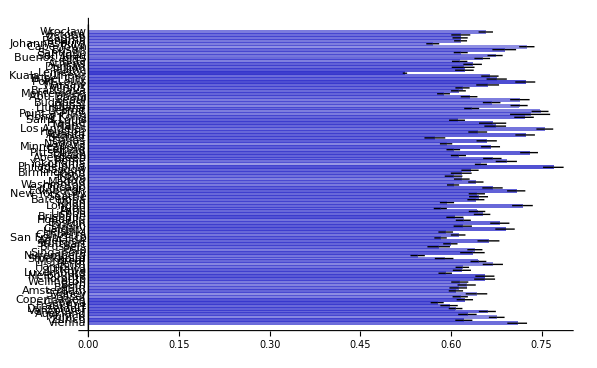

```mathematica
citiesColors = Map[RGBColor[0.2, 0.2, 0.8, #] &, citiesCertainties];
citiesPositivnessFromTweets = citiesEstimates⟦All, 1⟧;
BarChart[citiesPositivnessFromTweets,ChartLabels->Map[CityName, citiesPopular],BarOrigin->Left,ChartStyle->citiesColors]
```

As we can see, there is not much variance between cities, in terms of Tweets sentiment.
Lets compile multiple rankings together, assuming that they have had a more complete model for estimating the quality of life and satisfaction.

```mathematica
citiesPositivness = RescaleIntoInterval[Map[(N[1/#]) &, citiesWRanks⟦All, 2⟧]];
```

## Are there any correlations at all?

wew

```mathematica
NormalizeFeatures[rowsPerSample_List] := Module[{rowsPerFeature, rowsPerFeatureNormalized},
	rowsPerFeature = Transpose[rowsPerSample];
	rowsPerFeatureNormalized = Map[RescaleIntoInterval, rowsPerFeature];
	Transpose[rowsPerFeatureNormalized]
];
FitRegressionRect[rowsPerSample_, predictionsVals_] := Module[{inputNormalized, p, pLinearLayer, pWeights},
	p = Predict[rowsPerSample->predictionsVals, Method->"LinearRegression"];
	pLinearLayer = p⟦1, "Model", "MeanFunction"⟧;
	pWeights = Normal @ pLinearLayer⟦"Arrays"⟧⟦"Weights"⟧;
	pWeights
];
FitRegressionSquare[rowsPerSample_List, predictionsVals_List] := Inverse[Transpose[rowsPerSample].rowsPerSample].Transpose[rowsPerSample].predictionsVals;
RunRegression[weights_List, rowOfSample_List] := Total[Dot[weights, rowOfSample]];
FitRegression[rowsPerSample_, estimatesPerSample_, featuresNames_List] := Module[{
		inputTrain, inputValidate, outputTrain, outputValidate, outputEstimated, 
		modelWights, error, chart, result, trainingCount
	},
	trainingCount = Length[featuresNames];
	inputTrain = Take[rowsPerSample, trainingCount];
	outputTrain = Take[estimatesPerSample, trainingCount];
	inputValidate = Drop[rowsPerSample, trainingCount];
	outputValidate = Drop[estimatesPerSample, trainingCount];
	modelWights = FitRegressionSquare[inputTrain, outputTrain];
	outputEstimated = Map[(RunRegression[modelWights, #]) &, inputValidate];
	error = Norm[outputValidate-outputEstimated, 1] / Length[outputValidate];
	chart = BarChart[modelWights, ChartLabels->featuresNames, BarOrigin->Left];

	{error, chart, modelWights}
];
```

```mathematica
citiesFeatures = Map[ImportAllFeaturesClean[#] &, citiesPopular];
```

```mathematica
citiesFeaturesValues = NormalizeFeatures[Values[citiesFeatures⟦All⟧]]; (*Transform units into raw numbers.*)
citiesFeaturesNames = First[Keys[citiesFeatures⟦All⟧]];
```

```mathematica
citiesFeaturesValues = Map[Take[#, 40] &, citiesFeaturesValues]; (** Some features were not recognized.)
```

```mathematica
matCovs = Covariance[citiesFeaturesValues];
```

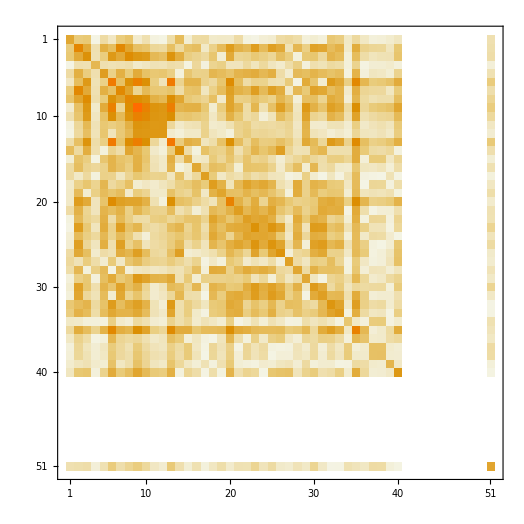

```mathematica
MatrixPlot[Abs[matCovs]]
```

```mathematica
m = FitRegression[citiesFeaturesValues, citiesPositivness, citiesFeaturesNames];
```

Inverse::sing: Matrix {{16.4203,23.7203,20.9834,15.3147,23.869,17.4913,23.6147,19.5378,18.7097,16.6486,16.3252,16.1903,«27»,15.1602,14.315,14.315,14.315,14.315,14.315,14.315,14.315,14.315,14.315,14.315,«1»},«49»,«1»} is singular.

General::stop: Further output of Inverse::sing will be suppressed during this calculation.

BarChart::ldata: Inverse[{{16.4203,23.7203,20.9834,15.3147,23.869,17.4913,23.6147,19.5378,18.7097,16.6486,16.3252,«29»,14.315,14.315,14.315,14.315,14.315,14.315,14.315,14.315,14.315,14.315,«1»},{23.7203,«49»,«1»},«48»,«1»}].«1» is not a valid dataset or list of datasets.

General::stop: Further output of BarChart::ldata will be suppressed during this calculation.

```mathematica
m
```

{1/49 (Abs[0.501768-RunRegression[Inverse[{1}].{15.3616,22.8078,20.0223,14.7346,22.8697,16.5601,22.7004,18.6439,35,13.7141,13.7141,13.7141,13.7141,13.7141,13.7141,13.7141,18.1041},{1}]]+47+Abs[1]),1,1}
 |  |  |  |

Lets compare the land use across region

```mathematica
BarChart[Lookup[ImportAllFeatures[city], Keys[statsAreaShareByPurpose]],ChartLabels->Keys[statsAreaShareByPurpose],BarOrigin->Left]
```

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

Import::chtype: First argument Hold[CityDataPath[/Users/ashvardanian/CodeMine/WolframSummer19/Data/Features,CityName[EntityValue[EntityValue[EntityValue[EntityValue[EntityValue[EntityValue[«2»],Name],Name],Name],Name],Name]]]] is not a valid file, directory, or URL specification.

Keys::invrl: The argument statsAreaShareByPurpose is not a valid Association or a list of rules.

Lookup::invrl: The argument $Failed is not a valid Association or a list of rules.

Keys::invrl: The argument statsAreaShareByPurpose is not a valid Association or a list of rules.

BarChart::ldata: Lookup[ImportAllFeatures[city],Keys[statsAreaShareByPurpose]] is not a valid dataset or list of datasets.

General::stop: Further output of BarChart::ldata will be suppressed during this calculation.

BarChart[Lookup[ImportAllFeatures[city],Keys[statsAreaShareByPurpose]],ChartLabels→Keys[statsAreaShareByPurpose],BarOrigin→Left]

## Are there correlations between cities topology and quality of life?

wewe

## Are there correlations between known features and quality of life?

wewe

```mathematica
BuildDataset[city_, rating_Real, imgs_] := Module[{ratings},
	ratings = Table[rating, Length[imgs]];(*Same for all images within city*)
	AssociationsFromPair[imgs, ratings]
];
```

```mathematica
datasetMaps = RandomSample[Flatten[MapThread[BuildDataset[#1, #2, ImportMaps[#1]] &, {citiesPopular, citiesPositivness}]]];
datasetSatellites = RandomSample[Flatten[MapThread[BuildDataset[#1, #2, ImportSatellites[#1]] &, {citiesPopular, citiesPositivness}]]];
```

```mathematica
datasetTrain = Take[datasetMaps, constantShareTraining * Length[datasetMaps]];
datasetValidate = Drop[datasetMaps, constantShareTraining * Length[datasetMaps]];
```

```mathematica
modelMapsANN = Predict[datasetTrain, Method->"NeuralNetwork", ValidationSet->datasetValidate, TrainingProgressReporting->"Panel"];
```

```mathematica
datasetTrain = Take[datasetSatellites, constantShareTraining * Length[datasetSatellites]];
datasetValidate = Drop[datasetSatellites, constantShareTraining * Length[datasetSatellites]];
```

```mathematica
modelSatellitesANN = Predict[datasetTrain, Method->"NeuralNetwork", ValidationSet->datasetValidate, TrainingProgressReporting->"Pwanel"];
```

$Aborted

```mathematica
Information[model]
```

```mathematica
cnnFull = NetModel["ResNet-101 Trained on YFCC100m Geotagged Data"];
```

```mathematica
modelGeoCNN = NetFlatten[NetChain[{NetTake[cnnFull, "pool1"], LinearLayer[{}], LogisticSigmoid}], 1]
```

NetChain[<>]

```mathematica
datasetTrain = Take[datasetSatellites, constantShareTraining * Length[datasetSatellites]];
datasetValidate = Drop[datasetSatellites, constantShareTraining * Length[datasetSatellites]];
```

```mathematica
modelGeoCNN = NetTrain[modelGeoCNN, Association[{"Input"->Keys[datasetTrain],"Output"->Values[datasetTrain]}], All]
```

NetChain[<>]